# Ques_02: Elementary functions.

Let

1. Introduce the above functions and do the graph using the Plot command. Choose a reasonable interval for the values of x .

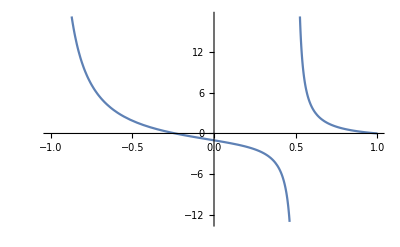

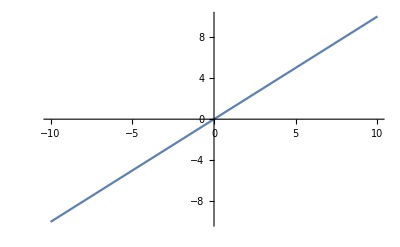

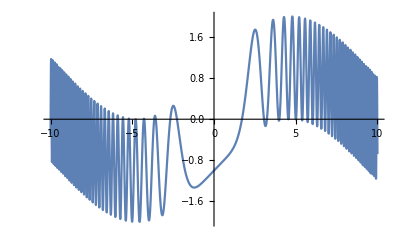

```mathematica
f[x_] :=(x^3 -5x^2 +3x+1)/(2x^2+x-1);
g[x_] := x;
h[x_] := Sin[x/3]-Cos[x^3/5]
Plot[f[x],{x,-1,1}]
Plot [x,{x,-10,10}]
Plot [h[x],{x,-10,10}]
```

2 .	g(x) is the  bisectrix of the first quadrant. Represent the graph of f(x) and g(x) in the same graph. There are three crossing points between both functions. Obtain graphically the point which is further away from the origin of the axis.

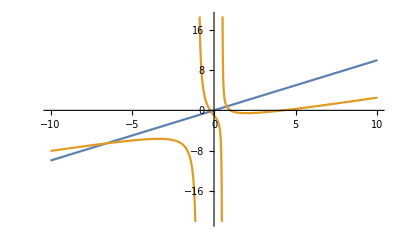

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)}}

```mathematica
Plot[{x,(x^3 -5x^2 +3x+1)/(2x^2+x-1)},{x,-10,10}]
Solve[{x(x^3 -5x^2 +3x+1)/(2x^2+x-1)},{x,y}]
```

Coordinate s of the point x= -6,5   , y= -6,9

3. 	Calculate the asymptotes of f[x]

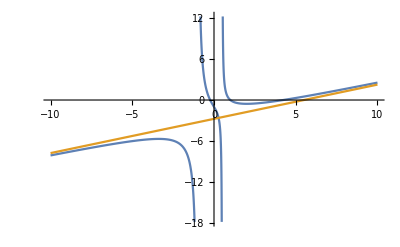

∞

1/2

-11/4

{{x→-1},{x→1/2}}

```mathematica
Plot[{f[x],(1x)/2-11/4},{x,-10,10}]
Limit[f[x],x->∞]
m=Limit[f[x]/x, x-> Infinity]
n=Limit[f[x]-1/2 x, x-> Infinity]
Solve[2x^2+x-1==0, {x}]
```

vertical  asymptotes:  x=  -1    ; x=1/2
                                 oblique asymptote: y=(1x)/2-11/4

4. 	Determine the symmetries of the functions f(x), g(x) and h(x), calculating  f(-x), g(-x) and h(-x). Obtain as a conclusion the symmetry of each function (even, odd or neither).

```mathematica
Simplify[(f[x]+f[-x])/2]
Simplify[f[x]]
Simplify[(x-x)/2]
Simplify[(h[x]+h[-x])/2]
Simplify[h[x]]
```

(-1+4 x^2-11 x^4)/(1-5 x^2+4 x^4)

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

0

-Cos[x^3/5]

-Cos[x^3/5]+Sin[x/3]

f(x) is  neither
                                     g(x) is  odd
                                    h(x) is  neither